```mathematica
Needs["ErrorBarPlots`"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Ag= Flatten[Import["../data/calibration/Ag.TKA","CSV"]];
Ba= Flatten[Import["../data/calibration/Ba.TKA","Table"]];
Cu= Flatten[Import["../data/calibration/Cu.TKA","Table"]];
Mo = Flatten[Import["../data/calibration/Mo.TKA","Table"]];
Rb=Flatten[Import["../data/calibration/Rb.TKA","Table"]];
Tb = Flatten[Import["../data/calibration/Tb.TKA","Table"]];
source = Flatten[Import["../data/calibration/source_nowindow.TKA","Table"]];
```

```mathematica
(*x = 100;
line1=Line[{{x,0},{x,150}}];
Prolog-> {Directive[{Thick,Red,Dashed}], line1}*)
```

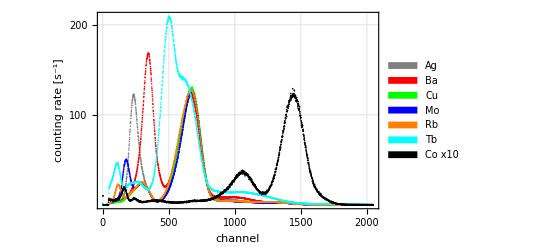

```mathematica
cobaltscale=10;
data = {Ag/300,Ba/300, Cu/300,Mo/300,Rb/300,Tb/300,source/300*cobaltscale};
plot=ListPlot[data,PlotRange->All,PlotStyle -> {Gray,Red,Green,Blue,Orange,Cyan,Black}, PlotLegends->SwatchLegend[{"Ag","Ba","Cu", "Mo", "Rb", "Tb", "Co x10"},LegendMarkerSize -> Automatic], AxesLabel -> {"Channel","Counting rate [s^-1]"},GridLines->{ 100Range[#2]&,Automatic},ImageSize->Full,Frame->True, FrameLabel-> {"channel","counting rate [s^-1]" },LabelStyle->{Black, Medium},FrameTicks->{{{100,200},{100,200}},{{0,500,1000,1500, 2000},None}}]
```

```mathematica
Export["../results/calibration/spectra.png",plot]
```

../results/calibration/spectrafinegrid.png

```mathematica
Clear[x]
```

```mathematica
peakpos={120,180,230,340,500};
speakpos = 10
peakenergy = {13.37,17.44,22.10,32.06,44.23};
datapoints=Transpose[{peakpos,peakenergy}];
```

10

```mathematica
?LinearModelFit
```

RowBox[{"LinearModelFit", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["y", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["x", "TI"]}], "]"}] constructs a linear model of the form RowBox[{SubscriptBox["β", "0"], "+", RowBox[{SubscriptBox["β", "1"], SubscriptBox[StyleBox["f", "TI"], "1"]}], "+", RowBox[{SubscriptBox["β", "2"], SubscriptBox[StyleBox["f", "TI"], "2"]}], "+", StyleBox["…", "TR"]}] that fits the SubscriptBox[StyleBox["y", "TI"], StyleBox["i", "TI"]] for successive StyleBox["x", "TI"] values 1, 2, ….
RowBox[{"LinearModelFit", "[", RowBox[{RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["11", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["12", "TR"]], ",", StyleBox["…", "TR"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["21", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["22", "TR"]], ",", StyleBox["…", "TR"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["2", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] constructs a linear model of the form RowBox[{SubscriptBox["β", "0"], "+", RowBox[{SubscriptBox["β", "1"], SubscriptBox[StyleBox["f", "TI"], "1"]}], "+", RowBox[{SubscriptBox["β", "2"], SubscriptBox[StyleBox["f", "TI"], "2"]}], "+", StyleBox["…", "TR"]}] where the SubscriptBox[StyleBox["f", "TI"], StyleBox["i", "TI"]] depend on the variables SubscriptBox[StyleBox["x", "TI"], StyleBox["k", "TI"]]. 
RowBox[{"LinearModelFit", "[", RowBox[{"{", RowBox[{StyleBox["m", "TI"], ",", StyleBox["v", "TI"]}], "}"}], "]"}] constructs a linear model from the design matrix StyleBox["m", "TI"] and response vector StyleBox["v", "TI"].

```mathematica
model = LinearModelFit[datapoints,x,x];
```

```mathematica
model["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 3.16552 | 0.627997 | 5.04067 | 0.0150542
x | 0.0827536 | 0.00205862 | 40.1986 | 0.0000338744

```mathematica
model["CovarianceMatrix"]//MatrixForm
```

(0.39438 | -0.00116119
-0.00116119 | 4.23791×10^-6)

```mathematica
modelplot =Plot[model["BestFit"],{x,0,500},Frame->True, FrameLabel-> {"channel","Energy [keV]" },LabelStyle->{Black, Medium},PlotStyle -> Red];
```

```mathematica
errorplot = ErrorListPlot[Table[{datapoints[[i]], ErrorBar[speakpos,0]},{i,1,5}]];
```

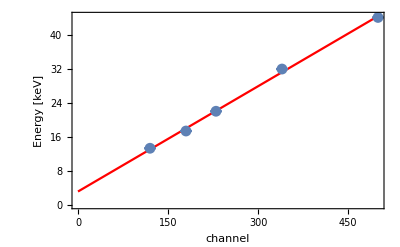

```mathematica
fitplot=Show[modelplot,errorplot]
```

```mathematica
Export["../results/calibration/fit.png",fitplot]
```

../results/calibration/fit.png

```mathematica
?ErrorListPlot
```

ErrorListPlot[{{y_1,dy_1},{y_2,dy_2},…}] plots points corresponding to a list of values y_1, y_2, …, with corresponding error bars. The errors have magnitudes dy_1,dy_2,….
ErrorListPlot[{{{x_1,y_1},ErrorBar[err_1]},{{x_2,y_2},ErrorBar[err_2]},…}] plots points with specified x and y coordinates and error magnitudes.

```mathematica
ch144=(14.4-3.2)/0.083
```

134.94

```mathematica
e=14.4;
a=0.083;
b=3.2;
```

```mathematica
sch144 = Sqrt[((e-b)/a^2)^2*0.002^2+(1/a^2)*0.6^2+2*(-0.001161187603690431)*((e-b)/a^2)*1/a]
```

4.16411